# UniDyn--Demo-Scratch.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  This demonstration notebook loads the UniDyn package and executes the package’s unit tests.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$UniDynPath ="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
```

/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn/UniDyn.m

Now that we are confident that the path is set correctly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True; (* Set to load quietly *)
Needs["UniDyn`"]
```

## Execute the units tests in batch

Included with the package are a number of files, ending in “-tests.m”, that contain tests of the package’s functions -- so-called unit tests.  Set the working directory to the package directory and pretty-print the directory name.

```mathematica
SetDirectory[$UniDynPath];
TableForm[{{$UniDynPath}},TableHeadings->{None,{"Directory"}}]
```

Directory
/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn

Get the names of all the unit-testing files included with the package (following my convention that the unit testing file end in “-tests.m”).   Pretty-print the names of the unit-test files included with the package.

```mathematica
fn = FileNames["*-tests.m"];
TableForm[{{fn}},TableHeadings->{None,{"Test files found"}}]
```

Test files found
Comm-tests.m
Evolve-tests.m
Mult-tests.m
OpQ-tests.m
Osc-tests.m
Spins-tests.m

Finally, carry out the unit tests and make a report.

```mathematica
test$report =TestReport /@ fn;
TableForm[Table[test$report[[k]],{k,1,Length[test$report]}]]
```

TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]

Make a report.

```mathematica
tests$passed$total = Plus @@ (test$report[[#]]["TestsSucceededCount"]& /@ List @@ Table[k,{k,1,Length[test$report]}]);
tests$failed$total = Plus @@ (test$report[[#]]["TestsFailedCount"]& /@ List @@ Table[k,{k,1,Length[test$report]}]);

Print[Style[ToString[tests$passed$total ] <> " tests passed",FontWeight-> Bold,FontSize-> 18,FontColor-> Blue]]
Print[Style[ToString[tests$failed$total ] <> " tests failed" ,FontWeight-> Bold,FontSize-> 18,FontColor-> Red]]
```

113 tests passed

0 tests failed

## Single spin: Taking repeated commutators

Create a  single-spin system to play with.

```mathematica
Needs["UniDyn`"];
Clear[H,Ix, Iy, Iz,Δ,ω]
CreateScalar[{Δ,ω}];
SpinSingle$CreateOperators[Ix, Iy, Iz];
```

SpinSingle$CreateOperators::create: Creating spin operators.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::nosimplify: No angular momentum L defined.

Define a Hamiltonian

```mathematica
H = Δ Iz + ω Ix;
```

### Repeated commutators

Define a function to take n commutators of an operator Op with the -i times the Hamiltonian H.

```mathematica
Clear[RepeatedComm];
RepeatedComm[1,H_,Op_] :=  List[Op];
RepeatedComm[n_,H_,Op_] :=  Prepend[RepeatedComm[n-1,H,Op],-I Comm[H,RepeatedComm[n-1,H,Op][[1]]]];
```

Example calculation of repeated commutators

```mathematica
σ = RepeatedComm[5,H,Iz] // Expand // Simplify;
σ // MatrixForm
```

(ω (-Ix Δ+Iz ω) (Δ^2+ω^2)
Iy ω (Δ^2+ω^2)
ω (Ix Δ-Iz ω)
-Iy ω
Iz)

### Evolution

Use the Evolver function to calculate the evolution of the I_x operator under the on-resonance Zeeman Hamiltonian first.

```mathematica
$Assumptions = {Δ ∈Reals,Δ > 0};
SetOptions[Evolver,quiet -> True]; (* Set this to False when debugging. *)
Evolver[Δ Iz,t,Ix]
```

Ix Cos[t Δ]+Iy Sin[t Δ]

As a check, use the Evolver function to calculate the evolution of the I_x operator under the off-resonance Zeeman Hamiltonian.

```mathematica
$Assumptions = {Δ ∈Reals,Δ > 0, ω ∈Reals, ω>= 0};
SetOptions[Evolver,quiet -> True]; (* Set this to False when debugging. *)
Evolver[H,t,Ix]
```

(ω (Iz Δ+Ix ω)+Δ (Ix Δ-Iz ω) Cos[t √(Δ^2+ω^2)]+Iy Δ √(Δ^2+ω^2) Sin[t √(Δ^2+ω^2)])/(Δ^2+ω^2)

Some simplification is needed to get a nice-looking answer.

```mathematica
$Assumptions = {Δ ∈Reals,Δ > 0, ω ∈Reals, ω>= 0};
ρ=Collect[Expand[Simplify[ExpToTrig[Evolver[H,t,Ix]]]],{Ix,Iy,Iz},Simplify]
```

(Ix (ω^2+Δ^2 Cos[t √(Δ^2+ω^2)]))/(Δ^2+ω^2)+(2 Iz Δ ω Sin[1/2 t √(Δ^2+ω^2)]^2)/(Δ^2+ω^2)+(Iy Δ Sin[t √(Δ^2+ω^2)])/(√(Δ^2+ω^2))

## Quantum optics

### Operators

```mathematica
Needs["UniDyn`"];
Clear[H,Ix, Iy, Iz,Δ,ω, g, F, aL,aR,Q$sym, P$sym, Q,P,QP$rules]
CreateScalar[{Δ,ω,Δω,g, F,ϕ}];
CreateOperator[{{Ix, Iy, Iz},{aL,aR}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, 1/2];
OscSingle$CreateOperators[aL,aR];

Q$sym=(aR+aL)/Sqrt[2];
P$sym =I (aR-aL)/Sqrt[2];
QP$rules = {aR -> (Q - I P)/Sqrt[2], aL -> (Q + I P)/Sqrt[2]};
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

OscSingle$CreateOperators::nocreate: Oscillator operators already exist.

OscSingle$CreateOperators::comm: Adding oscillator commutations relations.

```mathematica
Q$sym /. QP$rules // Simplify
P$sym /. QP$rules // Simplify
```

Q

P

### Hamiltonians

#### Free evolution

```mathematica
$Assumptions = {Element[ω, Reals], ω > 0};
H$0 = ω/2 (Mult[aR,aL] + Mult[aL,aR]);
```

```mathematica
Evolver[H$0,t,Q$sym]  /. QP$rules // ExpToTrig // Simplify
```

Q Cos[t ω]-P Sin[t ω]

#### Position or momentum kick

```mathematica
Clear[δx,δp];
$Assumptions = {Element[δx, Reals],Element[δp, Reals]};
H$0$x$kick = δx P$sym ;
H$0$p$kick = δp Q$sym;
```

```mathematica
Simplify[Evolver[H$0$x$kick ,t,Q$sym]  /. QP$rules ~Join~ {t-> 1}]  // Simplify
Simplify[Evolver[H$0$p$kick ,t,P$sym]  /. QP$rules ~Join~ {t-> 1}]  // Simplify
```

Q-δx

P+δp

#### Phase Kick

```mathematica
$Assumptions = {Element[ω, Reals], ω > 0};
H$0$phase$kick = (ω+Δω)/2 (Mult[aR,aL] + Mult[aL,aR]) ;
```

```mathematica
Simplify[Evolver[H$0$phase$kick,t,Q$sym]  /. QP$rules] /. {Δω-> Δϕ/t} // ExpToTrig // Simplify
```

Q Cos[Δϕ+t ω]-P Sin[Δϕ+t ω]

#### Force

```mathematica
$Assumptions = {Element[F, Reals], F > 0};
H$1 = - F Q$sym;
```

```mathematica
Simplify[Evolver[H$1,t,Q$sym] /. QP$rules ]
Simplify[Evolver[H$1,t,P$sym] /. QP$rules]
```

Q

P-F t

```mathematica
Simplify[Evolver[H$1,t,aR]]
Simplify[Evolver[H$1,t,aL]]
```

aR+(ⅈ F t)/(√2)

aL-(ⅈ F t)/(√2)

#### Squeezing

```mathematica
$Assumptions = {Element[Δ, Reals], Δ > 0, Element[ω, Reals], ω > 0};
```

```mathematica
Simplify[Evolver[-Δ/2 I (Mult[aR,aR] - Mult[aL,aL]),t,#]  /. QP$rules]& /@ {Q$sym, P$sym}
```

{ⅇ^(t Δ) Q,ⅇ^(-t Δ) P}

```mathematica
Simplify[Evolver[Δ/2 I (Mult[aR,aR] - Mult[aL,aL]),t,#]  /. QP$rules]& /@ {Q$sym, P$sym}
```

{ⅇ^(-t Δ) Q,ⅇ^(t Δ) P}

```mathematica
Expand[Simplify[ExpToTrig[Evolver[Δ/2 (Mult[aR,aR] + Mult[aL,aL]),t,#]  /. QP$rules]]]& /@ {Q$sym, P$sym}
```

{Q Cosh[t Δ]+P Sinh[t Δ],P Cosh[t Δ]+Q Sinh[t Δ]}

Let's remind ourselves what the hyperbolic functions look like

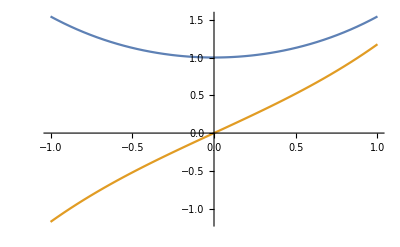

```mathematica
Plot[{Cosh[T],Sinh[T]},{T,-1,1}]
```

```mathematica
Collect[Simplify[ExpToTrig[Evolver[ ω/2 (Mult[aR,aL] + Mult[aL,aR])-Δ/2 I (Mult[aR,aR] - Mult[aL,aL]),t,#]  /. QP$rules]],{Q,P}]& /@ {Q$sym, P$sym}
```

{-(P ω Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))+Q (Cosh[t √(Δ^2-ω^2)]+(Δ Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))),(Q ω Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))+P (Cosh[t √(Δ^2-ω^2)]-(Δ Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2)))}

## Another quantum optics example

```mathematica
Needs["UniDyn`"];
Clear[λ,t, Ix, Iy, Iz,I$m, I$p,aL,aR, H];
CreateScalar[{λ,t}];
CreateOperator[{{Ix, Iy, Iz,I$m,I$p},{aL,aR}}];
OscSingle$CreateOperators[aL,aR];
```

OscSingle$CreateOperators::nocreate: Oscillator operators already exist.

OscSingle$CreateOperators::comm: Adding oscillator commutations relations.

```mathematica
I$p/:Comm[I$p,I$m]=2 Iz;
I$p/:Comm[I$p,Iz]=-I$p;
I$m/:Comm[I$m,I$p]=-2 Iz;
I$m/:Comm[I$m,Iz]=I$m;
Iz/:Comm[Iz,I$p]=I$p;
Iz/:Comm[Iz,I$m]=-I$m;
```

```mathematica
Iz/:NonCommutativeMultiply[a___,Iz,Iz,b___]:=1/4 Mult[a,b];
I$p/:Mult[a___,I$p,I$p,b___]:=0;
I$m/:Mult[a___,I$m,I$m,b___]:=0;

I$p/:Mult[a___,I$p,Iz,b___]:=- 1/2 Mult[a,I$p,b];
I$p/:Mult[a___,I$p,I$m,b___]:=1/2 Mult[a,b]+Mult[a,Iz,b];

I$m/:Mult[a___,I$m,Iz,b___]:= 1/2 Mult[a,I$m,b];
I$m/:Mult[a___,I$m,I$p,b___]:=1/2 Mult[a,b]-Mult[a,Iz,b];

I$z/:Mult[a___,I$z,Ip,b___]:=  1/2 Mult[a,I$p,b];
I$z/:Mult[a___,I$z,I$m,b___]:=-1/2 Mult[a,I$m,b];
```

```mathematica
H = λ(Mult[I$p,aL]+Mult[I$m,aR]);
Comm[I H,aL]
```

-ⅈ I$m λ

```mathematica
Comm[I H,Comm[I H,aL]]
```

2 λ^2 Mult[Iz,aL]

```mathematica
Comm[I H, aR]
```

ⅈ I$p λ

```mathematica
Comm[I H,Comm[I H,aR]]
```

2 λ^2 Mult[Iz,aR]

```mathematica
Comm[I H,Comm[I H,Comm[I H,aL]]]  // Simplify
```

-ⅈ λ^3 (I$m-2 Mult[I$m,aL,aR]+2 Mult[I$p,aL,aL])

```mathematica
Comm[I H, Comm[I H,Comm[I H,Comm[I H,aL]]] ] // Simplify
```

-λ^4 (3 aL-4 Mult[Iz,aL]+4 Mult[Iz,aL,aL,aR]+4 Mult[Iz,aL,aR,aL])

```mathematica
Evolver[λ Iz,t,I$p]
Evolver[λ Iz,t,I$m]
```

ⅇ^(-ⅈ t λ) I$p

ⅇ^(ⅈ t λ) I$m

```mathematica
Evolver[λ (Mult[I$p,aL]+Mult[I$m,aR]),t,aL] // Simplify
```

Evolver::unsolvable: Unrecognized evolution

{aL,ⅈ I$m λ,2 λ^2 Mult[Iz,aL],ⅈ λ^3 (I$m-2 Mult[I$m,aL,aR]+2 Mult[I$p,aL,aL]),-λ^4 (3 aL-4 Mult[Iz,aL]+4 Mult[Iz,aL,aL,aR]+4 Mult[Iz,aL,aR,aL])}

```mathematica
ⅈ λ^3 (I$m-2 Mult[I$m,aL,aR]+2 Mult[I$p,aL,aL]) /. Mult-> SortedMult
```

ⅈ λ^3 (I$m-2 Mult[I$m,aL,aR]+2 Mult[I$p,aL,aL])

```mathematica
Evolver[λ (Mult[I$m,aR]),t,aL] // Simplify
```

aL+ⅈ I$m t λ

```mathematica
Evolver[λ (Mult[I$p,aL]+Mult[I$m,aR]),t,(aL - aR)] // Simplify
```

Evolver::unsolvable: Unrecognized evolution

{aL-aR,ⅈ (I$m+I$p) λ,2 λ^2 (Mult[Iz,aL]-Mult[Iz,aR]),ⅈ λ^3 (I$m-I$p-2 Mult[I$m,aL,aR]+2 Mult[I$m,aR,aR]+2 Mult[I$p,aL,aL]-2 Mult[I$p,aR,aL]),-λ^4 (3 aL-3 aR-4 Mult[Iz,aL]-4 Mult[Iz,aR]+4 Mult[Iz,aL,aL,aR]+4 Mult[Iz,aL,aR,aL]-4 Mult[Iz,aR,aL,aR]-4 Mult[Iz,aR,aR,aL])}

## Failing cases

#### Off-resonance evolution of Iz is touchy

This Evolution broke in upgrading from Mathematica 10 to 11.  Figure out why.

```mathematica
Clear[Ix$sym, Iy$sym, Iz$sym, Sx$sym, Sy$sym, Sz$sym, ω, d$sym, Δ, rho$sym, t$sym]
Clear[A, r, lhs$list, rhs$list, time, eqns, system, rho$calc, rho$known, X]

CreateScalar[ω, d$sym, Δ];
CreateOperator[{{Ix$sym, Iy$sym, Iz$sym},{Sx$sym, Sy$sym, Sz$sym}}]

SpinSingle$CreateOperators[Ix$sym, Iy$sym, Iz$sym, L=1/2];
SpinSingle$CreateOperators[Sx$sym, Sy$sym, Sz$sym, L=1/2];
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

```mathematica
rho$known = Collect[
  constant1 Iz$sym + constant2 Ix$sym + (constant3 Iz$sym - constant2 Ix$sym) Cos[omega$eff t$sym] - constant4 Iy$sym Sin[omega$eff t$sym] // 
    Expand, {Ix$sym, Iy$sym, Iz$sym}];

rho$calc = Collect[
  Evolver[Δ Iz$sym + ω Ix$sym , t$sym, Iz$sym, quiet -> True] // FullSimplify, {Ix$sym, Iy$sym, Iz$sym},Expand];
```

```mathematica
rho$known
```

Ix$sym ((Δ ω)/(Δ^2+ω^2)-(Δ ω Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))+Iz$sym (Δ^2/(Δ^2+ω^2)+(ω^2 Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))-(Iy$sym ω Sin[t$sym √(Δ^2+ω^2)])/(√(Δ^2+ω^2))

```mathematica
rho$calc
```

Ix$sym ((Δ ω)/(Δ^2+ω^2)-(Δ ω Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))+Iz$sym (Δ^2/(Δ^2+ω^2)+(ω^2 Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))-(Iy$sym ω Sin[t$sym √(Δ^2+ω^2)])/(√(Δ^2+ω^2))

#### Force with a phase factor

This fails because Mathematica cannot recognize that Comm[aL ⅇ^(-i ϕ),aR]→  ⅇ^(-i ϕ) Comm[aL,aR]→ ⅇ^(-i ϕ).  Conclude that the Comm[] function is not yet smart enough to factor a function of scalar out of a commutator.

```mathematica
CreateScalar[{F,ϕ}];
$Assumptions = {Element[F, Reals], F > 0};
H$1 = F (Exp[-I ϕ] aL + Exp[I ϕ] aL );
```

```mathematica
Evolver[H$1,t,aR] // Simplify
```

aR-2 ⅈ F t Cos[ϕ]

## Quantum defect

```mathematica
Clear[Ix, Iy, Iz];
SpinSingle$CreateOperators[Ix, Iy, Iz];
```

SpinSingle$CreateOperators::create: Creating spin operators.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::nosimplify: No angular momentum L defined.

```mathematica
Evolver[ω Iz,t,Ix ]
```

Ix Cos[t ω]+Iy Sin[t ω]

```mathematica
Evolver[ω Iz,t,Mult[Ix,Ix]]
```

Cos[t ω]^2 Mult[Ix,Ix]+Sin[t ω] (Cos[t ω] (Mult[Ix,Iy]+Mult[Iy,Ix])+Mult[Iy,Iy] Sin[t ω])

```mathematica
Comm[Iz,Ix]
```

ⅈ Iy

Why won’t this expand?

```mathematica
Comm[Iz,Mult[Ix,Ix]]
```

ⅈ Mult[Ix,Iy]+ⅈ Mult[Iy,Ix]

Do the comm tests manually

```mathematica
Clear[a$sym,b$sym,c$sym,d$sym];
Clear[Ix$sym,Iy$sym,Iz$sym,Sx$sym,Sy$sym,Sz$sym];
Clear[A$sym,B$sym,C$sym,D$sym];

CreateScalar[{a$sym,b$sym,c$sym,d$sym}];
CreateOperator[{{Ix$sym,Iy$sym,Iz$sym},{Sx$sym,Sy$sym,Sz$sym}}];
```

Test 01a

```mathematica
Comm[Ix$sym,Iy$sym+Iz$sym]
```

Comm[Ix$sym,Iy$sym]+Comm[Ix$sym,Iz$sym]

Test 03b

```mathematica
Comm[a$sym Sx$sym,b$sym Mult[Sy$sym,Sz$sym]]
```

a$sym b$sym (Mult[Sy$sym,Comm[Sx$sym,Sz$sym]]+Mult[Comm[Sx$sym,Sy$sym],Sz$sym])

Why won't this expand?

```mathematica
Comm[ Iz$sym, Mult[Ix$sym,Iy$sym]]
```

Mult[Ix$sym,Comm[Iz$sym,Iy$sym]]+Mult[Comm[Iz$sym,Ix$sym],Iy$sym]

```mathematica
Clear[Ix, Iy, Iz];
SpinSingle$CreateOperators[Ix, Iy, Iz];
```

SpinSingle$CreateOperators::create: Creating spin operators.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::nosimplify: No angular momentum L defined.

```mathematica
Mult[Iz, Comm[Iz,Ix]] + Mult[Comm[Iz,Ix], Iz] // Simplify
```

ⅈ (Mult[Iy,Iz]+Mult[Iz,Iy])

```mathematica
Comm[Iz,Ix]
```

ⅈ Iy

What the hell?

```mathematica
Comm[ⅈ (Mult[Iy,Iz]+Mult[Iz,Iy]),Ix]  // Expand
```

-2 Mult[Iy,Iy]+2 Mult[Iz,Iz]

Why is this devolving to Power[]?

```mathematica
Comm[ⅈ (Mult[Iy,Iz]+Mult[Iz,Iy]),Ix]  // Expand
```

-2 Mult[Iy,Iy]+2 Mult[Iz,Iz]

```mathematica
Comm[ⅈ (Mult[Iy,Iz]+Mult[Iz,Iy]),Ix]
```

ⅈ (2 ⅈ Mult[Iy,Iy]-2 ⅈ Mult[Iz,Iz])